```mathematica
Table[1/k! D[1/(1-x),{x,k}]/.x->0,{k,0,10}]
```

{1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Table[1/k! D[1/(1+x),{x,k}]/.x->0,{k,0,10}]
```

{1,-1,1,-1,1,-1,1,-1,1,-1,1}

```mathematica
Table[1/k! D[Log[1/(1-x)],{x,k}]/.x->0,{k,0,10}]
```

{0,1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10}

```mathematica
Log[1/(1-x)]
```

Log[1/(1-x)]

```mathematica
Clear[sp]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
sp[n_,k_]:=sp[n,k]=Sum[PartitionsP[j]sp[n-j,k-1],{j,1,n}]
sp[n_,0]:=UnitStep[n]
sz[n_,z_]:=Sum[ bin[z,k] sp[n,k],{k,0,n}]
```

```mathematica
Table[Expand[sz[n,z]-sz[n-1,z]]/.z->-1,{n,1,20}]
```

{-1,-1,0,0,1,0,1,0,0,0,0,-1,0,0,-1,0,0,0,0,0}

```mathematica
Table[PartitionsP[n],{n,1,10}]
```

{1,2,3,5,7,11,15,22,30,42}

```mathematica
aa[n_]:=SeriesCoefficient[Product[1-x^k,{k,n}],{x,0,n}]
al[n_]:=SeriesCoefficient[Log[Product[1-x^k,{k,n}]],{x,0,n}]
```

```mathematica
Table[aa[j],{j,1,20}]
```

{-1,-1,0,0,1,0,1,0,0,0,0,-1,0,0,-1,0,0,0,0,0}

```mathematica
Table[al[j],{j,1,20}]
```

{-1,-3/2,-4/3,-7/4,-6/5,-2,-8/7,-15/8,-13/9,-9/5,-12/11,-7/3,-14/13,-12/7,-8/5,-31/16,-18/17,-13/6,-20/19,-21/10}

```mathematica
Table[-DivisorSigma[1,j]/j,{j,1,20}]
```

{-1,-3/2,-4/3,-7/4,-6/5,-2,-8/7,-15/8,-13/9,-9/5,-12/11,-7/3,-14/13,-12/7,-8/5,-31/16,-18/17,-13/6,-20/19,-21/10}

```mathematica
Table[FullSimplify[1/k! D[(1/(1-x)-1)^z,{x,k}]]/.x->0,{k,0,6}]
```

{0^z,0^(-1+z) z,1/2 0^(-2+z) (-1+z) z,1/6 0^(-3+z) z (2-3 z+z^2),1/24 0^(-4+z) (-3+z) (-2+z) (-1+z) z,1/120 0^(-5+z) (-4+z) (-3+z) (-2+z) (-1+z) z,1/720 0^(-6+z) (-5+z) (-4+z) (-3+z) (-2+z) (-1+z) z}

```mathematica
((x/(1-x))^(-1+z) z)/(-1+x)^2/.x->0
```

0^(-1+z) z

```mathematica
Clear[lb]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
lb[n_,k_,f_]:=lb[n,k,f]=Sum[f[j]lb[n-j,k-1,f],{j,1,n}]
lb[n_,0,f_]:=UnitStep[n]
llb[n_,f_]:=Sum[(-1)^(k+1)/k lb[n,k,f],{k,1,n}]
lbz[n_,z_,f_]:=Sum[bin[z,k]lb[n,k,f],{k,0,n}]
llz[n_,z_,f_]:=Sin[Pi z]/Pi Sum[ (-1)^k / (z-k) lb[n,k,f],{k,0,n}]
lroots[n_,ff_]:=If[(c=Exponent[f=(lbz[n,z,ff]),z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
dlroots[n_,ff_]:=If[(c=Exponent[f=(lbz[n,z,ff]-lbz[n-1,z,ff]),z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
bpoly[n_,z_,ff_]:=Expand@FullSimplify@Expand[llz[n,z,ff]/(Sin[Pi z]/Pi)FactorialPower[z,n+1] ]
dbpoly[n_,z_,ff_]:=Expand@FullSimplify@Expand[(llz[n,z,ff]-llz[n-1,z,ff])/(Sin[Pi z]/Pi)FactorialPower[z,n+1] ]
l2roots[n_,ff_]:=If[(c=Exponent[f=(bpoly[n,z,ff]),z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
dl2roots[n_,ff_]:=If[(c=Exponent[f=(dbpoly[n,z,ff]),z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
```

```mathematica
id[n_]:=1
idd[n_]:=PartitionsP[n]
```

```mathematica
lb[10,3,idd]
```

2544

```mathematica
lbz[10,3,idd]
```

5773

```mathematica
llb[10,idd]
```

7583/504

```mathematica
Expand[llz[10,z,idd]]
```

Sin[π z]/(π (-10+z))-(19 Sin[π z])/(π (-9+z))+(153 Sin[π z])/(π (-8+z))-(687 Sin[π z])/(π (-7+z))+(1898 Sin[π z])/(π (-6+z))-(3343 Sin[π z])/(π (-5+z))+(3741 Sin[π z])/(π (-4+z))-(2544 Sin[π z])/(π (-3+z))+(938 Sin[π z])/(π (-2+z))-(138 Sin[π z])/(π (-1+z))+Sin[π z]/(π z)

```mathematica
Sum[PartitionsP[j],{j,1,10}]
```

138

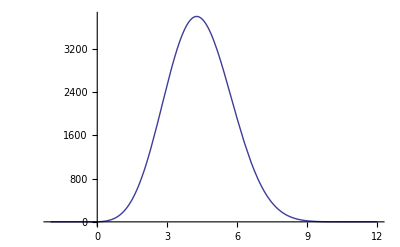

```mathematica
Plot[llz[10,z,idd],{z,-2,12}]
```

```mathematica
Expand[lbz[10,z,idd]]
```

1+(7583 z)/504+(750731 z^2)/16800+(8720689 z^3)/181440+(1708153 z^4)/72576+(201641 z^5)/34560+(133993 z^6)/172800+(6779 z^7)/120960+(13 z^8)/6048+(29 z^9)/725760+z^10/3628800

```mathematica
FullSimplify@Product[1-1/r,{r,lroots[10,id]}]
```

11

```mathematica
lbz[10,1,id]
```

11

```mathematica
bpoly[n_,z_,ff_]:=Expand@FullSimplify@Expand[llz[n,z,ff]/(Sin[Pi z]/Pi)FactorialPower[z,n+1] ]
```

```mathematica
Limit[bpoly[10,z,id]/FactorialPower[z,11] Sin[Pi z]/Pi,z->1]
```

10

```mathematica
N@l2roots[10,idd]
```

{-0.920496,-0.0856497,2.08088-6.96201 ⅈ,2.08088+6.96201 ⅈ,7.16714-5.02105 ⅈ,7.16714+5.02105 ⅈ,9.56332-2.74592 ⅈ,9.56332+2.74592 ⅈ,10.6917-0.821476 ⅈ,10.6917+0.821476 ⅈ}

```mathematica
Clear[rb]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
rb[n_,k_,f_]:=rb[n,k,f]=Sum[f[j]rb[Floor[n/j],k-1,f],{j,2,n}]
rb[n_,0,f_]:=UnitStep[n-1]
lrb[n_,f_]:=Sum[(-1)^(k+1)/k rb[n,k,f],{k,1,Log2@n}]
rbz[n_,z_,f_]:=Sum[bin[z,k]rb[n,k,f],{k,0,Log2@n}]
lrz[n_,z_,f_]:=Sin[Pi z]/Pi Sum[ (-1)^k / (z-k) rb[n,k,f],{k,0,Log2@n}]
rlroots[n_,ff_]:=If[(c=Exponent[f=(rbz[n,z,ff]),z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
rdlroots[n_,ff_]:=If[(c=Exponent[f=(rbz[n,z,ff]-rbz[n-1,z,ff]),z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
rbpoly[n_,z_,ff_]:=Expand@FullSimplify@Expand[lrz[n,z,ff]/(Sin[Pi z]/Pi)FactorialPower[z,Floor[Log2@n]+1] ]
rbpolya[n_,z_,ff_]:=FullSimplify[lrz[n,z,ff]Floor[Log2@n]!/Binomial[Floor[Log2@n],z]]
rbpolyb[n_,z_,ff_]:=lrz[n,z,ff]/FactorialPower[z,Floor[Log2@n]]
rdbpoly[n_,z_,ff_]:=Expand@FullSimplify@Expand[(lrz[n,z,ff]-lrz[n-1,z,ff])/(Sin[Pi z]/Pi)FactorialPower[z,Floor[Log2@n]+1] ]
rl2roots[n_,ff_]:=If[(c=Exponent[f=(rbpoly[n,z,ff]),z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
rl2rootsa[n_,ff_]:=If[(c=Exponent[f=(rbpolya[n,z,ff]),z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
rdl2roots[n_,ff_]:=If[(c=Exponent[f=(rdbpoly[n,z,ff]),z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
```

```mathematica
Expand@lrz[100,z,id]
```

(7 Sin[π z])/(π (-6+z))-(51 Sin[π z])/(π (-5+z))+(184 Sin[π z])/(π (-4+z))-(324 Sin[π z])/(π (-3+z))+(283 Sin[π z])/(π (-2+z))-(99 Sin[π z])/(π (-1+z))+Sin[π z]/(π z)

```mathematica
Limit[FullSimplify[6!Product[1-z/r,{r,rl2roots[100,id]}]Sin[Pi z]/Pi / FactorialPower[z,7]],z->1/2]
```

113678/(1155 π)

```mathematica
Limit[(FullSimplify[6!Product[1-z/r,{r,rl2roots[100,id]}]Sin[Pi z]/Pi / FactorialPower[z,7]]-1)/z,z->0]
```

428/15

```mathematica
FullSimplify@Sum[-1/r,{r,rl2roots[100,id]}]
```

313/12

```mathematica
Limit[(FullSimplify[6!Sin[Pi z]/Pi / FactorialPower[z,7]]-1)/z,z->0]
```

49/20

```mathematica
HarmonicNumber[Floor[Log2@100]]
```

49/20

```mathematica
(D[Expand[rbpolya[100,z,id]],z]/.z->0)/6!
```

313/12

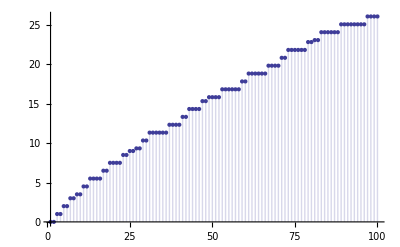

```mathematica
DiscretePlot[Re@Chop@N@Sum[-1/r,{r,rl2rootsa[n,id]}],{n,1,100}]
```

```mathematica
Expand@FullSimplify[lrz[100,z,id]/Sin[Pi z]*Pi * FactorialPower[z,7]]
```

720+18780 z-9400 z^2+1947 z^3-165 z^4-3 z^5+z^6

```mathematica
rbpoly[100,z,id]
```

720+18780 z-9400 z^2+1947 z^3-165 z^4-3 z^5+z^6

```mathematica
N@Sum[-1/r,{r,rl2roots[100,id]}]
```

26.0833+0. ⅈ

```mathematica
{N@Product[1-z/r,{r,rl2roots[100,id]}]Binomial[6,z]/.z->-1/2,N@lrz[100,-1/2,id]}
```

{-3.39902+0. ⅈ,-3.39902}

```mathematica
Table[6! Limit[Sin[Pi z]/Pi /FactorialPower[z,7],z->n],{n,0,6}]
```

{1,6,15,20,15,6,1}

```mathematica
Table[Binomial[6,k],{k,0,6}]
```

{1,6,15,20,15,6,1}

```mathematica
rbpoly[100,z,id]
```

720+18780 z-9400 z^2+1947 z^3-165 z^4-3 z^5+z^6

```mathematica
Limit[D[rbpolya[100,z,id],z],z->0]
```

18780

```mathematica
FullSimplify[n!/Binomial[n,z]]
```

(n!)/Binomial[n,z]

```mathematica
Expand@FullSimplify@rbpolya[10,z,id]
```

6+21 z-10 z^2+z^3

```mathematica
lrz[n_,z_,f_]:=Sin[Pi z]/Pi Sum[ (-1)^k / (z-k) rb[n,k,f],{k,0,Log2@n}]
rbpoly[n_,z_,ff_]:=Expand@FullSimplify@Expand[lrz[n,z,ff]/(Sin[Pi z]/Pi)FactorialPower[z,Floor[Log2@n]+1] ]
rbpolyx[n_,z_,ff_]:= Expand@FullSimplify@Expand[Sin[Pi z]/Pi Sum[ (-1)^k / (z-k) rb[n,k,ff],{k,0,Log2@n}]/(Sin[Pi z]/Pi)FactorialPower[z,Floor[Log2@n]+1] ]
rbpolyy[n_,z_,ff_]:= Sum[ (-1)^k  FactorialPower[z,Floor[Log2@n]+1]/ (z-k) rb[n,k,ff],{k,0,Log2@n}]
rbpolyy2[n_,z_,ff_]:= Sum[ (-1)^k / (z-k) rb[n,k,ff],{k,0,Log2@n}]
lrza[n_,z_,f_]:=rbpolyy[n,z,f]Binomial[Floor[Log2@n],z]/Floor[Log2@n]!
```

```mathematica
Expand@FullSimplify@Expand@rbpolyy[100,z,id]
```

720+18780 z-9400 z^2+1947 z^3-165 z^4-3 z^5+z^6

```mathematica
rbpoly[10,z,id]
```

-6-21 z+10 z^2-z^3

```mathematica
(-1)^k Floor[Log2@n+1]!/Binomial[z,Floor[Log2@n]+1] / (z-k)
```

((-1)^k (1+Floor[Log[n]/Log[2]])!)/((-k+z) Binomial[z,1+Floor[Log[n]/Log[2]]])

```mathematica
FullSimplify@lrza[100,z,id]/.z->2
```

283

```mathematica
Table[{n,Chop@N[Sum[-1/r,{r,rl2rootsa[n,id]}]-Sum[-1/r,{r,rl2rootsa[n-1,id]}]]},{n,1,100}]//TableForm
```

1 | 0
2 | 0
3 | 1.
4 | 0
5 | 1.
6 | 0
7 | 1.
8 | 0
9 | 0.5
10 | 0
11 | 1.
12 | 0
13 | 1.
14 | 0
15 | 0
16 | 0
17 | 1.
18 | 0
19 | 1.
20 | 0
21 | 0
22 | 0
23 | 1.
24 | 0
25 | 0.5
26 | 0
27 | 0.333333
28 | 0
29 | 1.
30 | 0
31 | 1.
32 | 0
33 | 0
34 | 0
35 | 0
36 | 0
37 | 1.
38 | 0
39 | 0
40 | 0
41 | 1.
42 | 0
43 | 1.
44 | 0
45 | 0
46 | 0
47 | 1.
48 | 0
49 | 0.5
50 | 0
51 | 0
52 | 0
53 | 1.
54 | 0
55 | 0
56 | 0
57 | 0
58 | 0
59 | 1.
60 | 0
61 | 1.
62 | 0
63 | 0
64 | 0
65 | 0
66 | 0
67 | 1.
68 | 0
69 | 0
70 | 0
71 | 1.
72 | 0
73 | 1.
74 | 0
75 | 0
76 | 0
77 | 0
78 | 0
79 | 1.
80 | 0
81 | 0.25
82 | 0
83 | 1.
84 | 0
85 | 0
86 | 0
87 | 0
88 | 0
89 | 1.
90 | 0
91 | 0
92 | 0
93 | 0
94 | 0
95 | 0
96 | 0
97 | 1.
98 | 0
99 | 0
100 | 0

```mathematica
mm[z_]:=7/(-6+z)-51/(-5+z)+184/(-4+z)-324/(-3+z)+283/(-2+z)-99/(-1+z)+1/z
```

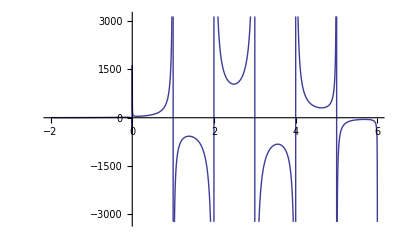

```mathematica
Plot[mm[z],{z,-2,6}]
```

```mathematica
Residue[mm[z],{z,0}]
```

1

```mathematica
Expand@lrz[100,z,id]
```

(7 Sin[π z])/(π (-6+z))-(51 Sin[π z])/(π (-5+z))+(184 Sin[π z])/(π (-4+z))-(324 Sin[π z])/(π (-3+z))+(283 Sin[π z])/(π (-2+z))-(99 Sin[π z])/(π (-1+z))+Sin[π z]/(π z)

```mathematica
FullSimplify[1/Gamma[z]/Gamma[1-z]]
```

Sin[π z]/π

```mathematica
1/Gamma[5-z]/Gamma[z]/.z->2.3
```

0.554876

```mathematica
1/Gamma[z]/Gamma[4-z]/(4-z)/.z->2.3
```

0.554876

```mathematica
1/Gamma[z]/Gamma[1-z]/(4-z)/(3-z)/(2-z)/(1-z)/.z->2.3
```

0.554876

```mathematica
Sin[Pi z]/Pi /(4-z)/(3-z)/(2-z)/(1-z)/.z->2.3
```

0.554876

```mathematica
Sin[Pi z]/Pi /FactorialPower[z-1,4]/.z->2.3
```

0.554876